```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
DefineDottedIndices
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F,U,H,g,τ,v,H,m,μ,Q},1},
{{y,U,u,ψ,V,h,H},2},
{{σ,λ,T},3},
{{σ},4}
]
```

Lecture 10 Oct 2011 notes

```mathematica
PR1["Higgs Potential in MSSM: ",
(tmpH={Hd[d][Y->-1/2]->{{Hdu[1,0]},{Hdu[1,"-"]}},
Hd[u][Y->1/2]->{{Hdu[2,"+"]},{Hdu[2,0]}}
})//MatrixForms,NL,
"Take potential",yield,tmpW=W->μ.Hd[u].Hd[d],Imply,
tmpV=V->μ^2 (SuperDagger[Hd[1]].Hd[1]+SuperDagger[Hd[2]].Hd[2])+g'^2/2 (SuperDagger[Hd[1]].(-1/2).Hd[1]+SuperDagger[Hd[2]].(1/2).Hd[2])^2+g^2/2 (SuperDagger[Hd[1]].(τ⃗/2).Hd[1]+SuperDagger[Hd[2]].(τ⃗/2).Hd[2])^2+md[Hd[1]]^2 SuperDagger[Hd[1]].Hd[1]+md[Hd[2]]^2 SuperDagger[Hd[2]].Hd[2]+(tmp=md[3]^2 Hd[2]∘Hd[1])+HC[tmp],NL,
" where the terms with ",{"g and g' coefficient are the D-terms.","m's are soft SSB terms "}//Column,NL,
"CP is not violated at least here.  Phase can exist in the md[3] term. Don't know if there is a phase in Hd[1]Hd[2] terms. Choose md[1], md[2], md[3] such that md[3]^2<0 because it would minimize the md[3] term.  The parameters {μ, md[Hd[1]], md[Hd[2]]} are sometimes recombined so that ",
tmpV1=V->μd[1]^2 SuperDagger[Hd[1]].Hd[1]+μd[2]^2 SuperDagger[Hd[2]].Hd[2]+μd[3]^2 (Hd[2]∘Hd[1]+HC[Hd[2]∘Hd[1]]),NL,

"Show relationship between ",{μd[1],μd[2],μd[3]}⟷{μ,md[Hd[1]],md[Hd[2]]}," when ",sub={g'->0,g->0},
tmp=tmpV;
tmp=tmp/.sub/.HC[a_ m_^2]->m^2 HC[a],Yield,
tmp=tmpV1[[2]]==tmp[[2]]//Simplify,NL,
"Taking the coefficients of ",tmpc={SuperDagger[(Subscript[H, 1]^1)].Subscript[H, 1]^1 ,SuperDagger[(Subscript[H, 2]^2)].Subscript[H, 2]^2 ,HC[Hd[2]∘Hd[1]]+Hd[2]∘Hd[1]},yield,
tmp1=Coefficient[tmp[[1]],tmpc]," to be 0 defines ",{μd[1],μd[2],μd[3]},Yield,
tmp=MapThread[Solve[#1==0,#2][[1]]&,{tmp1,{μd[1],μd[2],μd[3]}}]//Flatten;yield,
subμ=Map[TimesRules[{#,#}]&,tmp]
];
tmpV2=V->tmpV1[[2]]+Apply[Plus,ExtractPattern[tmpV,a__ (g|g')^2]]
Save[SaveFile,{tmpV,tmpV1,tmpV2,subμ}]
```

Higgs Potential in MSSM: {H_d^d[Y→-1/2]→(H_10^10
H_(1-)^(1-)),H_u^u[Y→1/2]→(H_(2+)^(2+)
H_20^20)}
Take potential ⟶ W→μ.H_u^u.H_d^d
⇒ V→μ^2 ((H_1^1)^†.H_1^1+(H_2^2)^†.H_2^2)+1/2 g^2 ((H_1^1)^†.(τ⃗)/2.H_1^1+(H_2^2)^†.(τ⃗)/2.H_2^2)^2+HC[H_2^2∘H_1^1 (m_3^3)^2]+H_2^2∘H_1^1 (m_3^3)^2+(H_1^1)^†.H_1^1 (m_(H_1^1)^(H_1^1))^2+(H_2^2)^†.H_2^2 (m_(H_2^2)^(H_2^2))^2+1/2 ((H_1^1)^†.(-1/2).H_1^1+(H_2^2)^†.1/2.H_2^2)^2 (g')^2
 where the terms with g and g' coefficient are the D-terms.
m's are soft SSB terms 
CP is not violated at least here.  Phase can exist in the md[3] term. Don't know if there is a phase in Hd[1]Hd[2] terms. Choose md[1], md[2], md[3] such that md[3]^2<0 because it would minimize the md[3] term.  The parameters {μ, md[Hd[1]], md[Hd[2]]} are sometimes recombined so that V→(H_1^1)^†.H_1^1 (μ_1^1)^2+(H_2^2)^†.H_2^2 (μ_2^2)^2+(HC[H_2^2∘H_1^1]+H_2^2∘H_1^1) (μ_3^3)^2
Show relationship between {μ_1^1,μ_2^2,μ_3^3}⟷{μ,m_(H_1^1)^(H_1^1),m_(H_2^2)^(H_2^2)} when {g'→0,g→0}V→μ^2 ((H_1^1)^†.H_1^1+(H_2^2)^†.H_2^2)+HC[H_2^2∘H_1^1] (m_3^3)^2+H_2^2∘H_1^1 (m_3^3)^2+(H_1^1)^†.H_1^1 (m_(H_1^1)^(H_1^1))^2+(H_2^2)^†.H_2^2 (m_(H_2^2)^(H_2^2))^2
→ (H_1^1)^†.H_1^1 (μ^2+(m_(H_1^1)^(H_1^1))^2-(μ_1^1)^2)+(H_2^2)^†.H_2^2 (μ^2+(m_(H_2^2)^(H_2^2))^2-(μ_2^2)^2)+(HC[H_2^2∘H_1^1]+H_2^2∘H_1^1) ((m_3^3)^2-(μ_3^3)^2)==0
Taking the coefficients of {(H_1^1)^†.H_1^1,(H_2^2)^†.H_2^2,HC[H_2^2∘H_1^1]+H_2^2∘H_1^1} ⟶ {μ^2+(m_(H_1^1)^(H_1^1))^2-(μ_1^1)^2,μ^2+(m_(H_2^2)^(H_2^2))^2-(μ_2^2)^2,(m_3^3)^2-(μ_3^3)^2} to be 0 defines {μ_1^1,μ_2^2,μ_3^3}
→  ⟶ {(μ_1^1)^2→μ^2+(m_(H_1^1)^(H_1^1))^2,(μ_2^2)^2→μ^2+(m_(H_2^2)^(H_2^2))^2,(μ_3^3)^2→(m_3^3)^2}

V→1/2 g^2 ((H_1^1)^†.(τ⃗)/2.H_1^1+(H_2^2)^†.(τ⃗)/2.H_2^2)^2+(H_1^1)^†.H_1^1 (μ_1^1)^2+(H_2^2)^†.H_2^2 (μ_2^2)^2+(HC[H_2^2∘H_1^1]+H_2^2∘H_1^1) (μ_3^3)^2+1/2 ((H_1^1)^†.(-1/2).H_1^1+(H_2^2)^†.1/2.H_2^2)^2 (g')^2

```mathematica
PR1["For single doublet with VEV:",yield,
(tmpv={Hd[1]->{{vd[1]},{0}},Hd[2]->{{vd[3]},{vd[2]}}})//MatrixForms,NL,
"Show vd[3]->0!  Is there a phase for vd[2]?  Suppose: ",sub=vd[2]->Abs[vd[2]]Exp[I α],Imply,
"terms in ",
V->μd[3].vd[1].Abs[vd[2]]Exp[-I α]+μd[3].vd[1].Abs[vd[2]]Exp[I α]∼Cos[α]," Choose α->0 then CP OK"
]
```

For single doublet with VEV: ⟶ {H_1^1→(v_1^1
0),H_2^2→(v_3^3
v_2^2)}
Show vd[3]->0!  Is there a phase for vd[2]?  Suppose: v_2^2→ⅇ^(ⅈ α) Abs[v_2^2]
⇒ terms in V→ⅇ^(-ⅈ α) μ_3^3.v_1^1.Abs[v_2^2]+ⅇ^(ⅈ α) μ_3^3.v_1^1.Abs[v_2^2]∼Cos[α] Choose α->0 then CP OK

```mathematica
PR1["Minimize the potential ",
tmpV=V->μd[1]^2 vd[1]^2+μd[2]^2 vd[2]^2-2 μd[3]^2 vd[1] vd[2]+g'^2/8 (vd[1]^2-vd[2]^2)^2+g^2/8 (vd[1]^2-vd[2]^2)^2,
" wrt ",{vd[1],vd[2]} ,Imply,
(tmpVmin={Map[xPartialD[#,vd[1]]&,tmpV]->0,
Map[xPartialD[#,vd[2]]&,tmpV]->0})//Column,NL,
"Gives minimization condition: ",Yield,
tmp=tmpVmin//DerivativeExpand[{g,g',μd[_]}];
tmp0=tmp/.xPartialD[vd[a_],vd[b_]]:>0/;a=!=b;
tmp0=Map[#[[1,2]]->#[[2]]&,tmp0],Yield,
tmp=Eliminate[(tmp0/.Rule->Equal),{g,g'}]//Simplify,Yield,
tmpfact=Apply[Times,ExtractPattern[tmp,(a_^2+b_^2)]];Yield,
tmpVmin1=Map[#/tmpfact&,tmp],NL,
"The other constraint is: ",
tmp={Map[# vd[1] &,tmp0[[1]]],Map[# vd[2] &,tmp0[[2]]]};
tmp=SubtractRules[tmp]/.Rule->Equal//Simplify;
tmpVmin2=Collect[tmp,{vd[1],vd[2]}]
];
Save[SaveFile,{tmpVmin1,tmpVmin2}]
```

Minimize the potential V→1/8 g^2 ((v_1^1)^2-(v_2^2)^2)^2+(v_1^1)^2 (μ_1^1)^2+(v_2^2)^2 (μ_2^2)^2-2 v_1^1 v_2^2 (μ_3^3)^2+1/8 ((v_1^1)^2-(v_2^2)^2)^2 (g')^2 wrt {v_1^1,v_2^2}
⇒ (UnderBar[∂]_(v_1^1)[V]→UnderBar[∂]_(v_1^1)[1/8 g^2 ((v_1^1)^2-(v_2^2)^2)^2+(v_1^1)^2 (μ_1^1)^2+(v_2^2)^2 (μ_2^2)^2-2 v_1^1 v_2^2 (μ_3^3)^2+1/8 ((v_1^1)^2-(v_2^2)^2)^2 (g')^2])→0
(UnderBar[∂]_(v_2^2)[V]→UnderBar[∂]_(v_2^2)[1/8 g^2 ((v_1^1)^2-(v_2^2)^2)^2+(v_1^1)^2 (μ_1^1)^2+(v_2^2)^2 (μ_2^2)^2-2 v_1^1 v_2^2 (μ_3^3)^2+1/8 ((v_1^1)^2-(v_2^2)^2)^2 (g')^2])→0
Gives minimization condition: 
→ {1/2 g^2 v_1^1 ((v_1^1)^2-(v_2^2)^2)+2 v_1^1 (μ_1^1)^2-2 v_2^2 (μ_3^3)^2+1/2 v_1^1 ((v_1^1)^2-(v_2^2)^2) (g')^2→0,-1/2 g^2 v_2^2 ((v_1^1)^2-(v_2^2)^2)+2 v_2^2 (μ_2^2)^2-2 v_1^1 (μ_3^3)^2-1/2 v_2^2 ((v_1^1)^2-(v_2^2)^2) (g')^2→0}
→ ((v_1^1)^2+(v_2^2)^2) (μ_3^3)^2==v_1^1 v_2^2 ((μ_1^1)^2+(μ_2^2)^2)
→ 
→ ((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)==(v_1^1 v_2^2)/((v_1^1)^2+(v_2^2)^2)
The other constraint is: 4 (v_1^1)^2 (μ_1^1)^2+(v_1^1)^4 (g^2+(g')^2)==4 (v_2^2)^2 (μ_2^2)^2+(v_2^2)^4 (g^2+(g')^2)

```mathematica
PR1["Ratio of vev's often defined: ",subβ=Tan[β]->vd[2]/vd[1],NL,
"Minimum condition becomes using the first constraint: ",
tmpβμ=tmpVmin1/.RuleX[subβ,vd[2]]//Simplify//TrigReduce,NL,
"where β can be restricted to the first quadrant.  For Sin[2β] to be Real and >0 ",imply,
tmpβμ1=tmpβμ/.Sin[_]->1/.Equal->LessEqual,NL,
"The second constraint can be rewritten: ",NL,
tmpVmin2,NL,"For Mathematica let ",sub=(a_^2+b_^2)->g2[(a^2+b^2)],Imply,
tmp=tmpVmin2/.sub/.Equal[a_,b_]->Equal[a-b,0]//Collect[#,g2[_]]&,Yield,
tmp=tmp/.(a_^4-b_^4):>Factor[(a^4-b^4)],NL,
"And note that ",sub=g2[a_](v1_^2+v2_^2)->2 md[Z]^2,Yield,
tmp=tmp/.sub//Simplify,Yield,
tmp=Solve[tmp,md[Z]][[2]];
tmp=TimesRules[Flatten[{tmp,tmp}]],yield,
tmpβμ2=tmp/.RuleX[subβ,vd[2]]//Simplify,NL,
"Giving a relationship between Tan[β],md[Z] and the μ's.  Recall that ",md[Hu["+"]]^2↔μd[1]^2±μd[2]^2
];
Save[SaveFile,{tmpβμ,tmpβμ1,tmpβμ2}]
```

Ratio of vev's often defined: Tan[β]→v_2^2/v_1^1
Minimum condition becomes using the first constraint: ((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)==1/2 Sin[2 β]
where β can be restricted to the first quadrant.  For Sin[2β] to be Real and >0  ⇒ ((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)≤1/2
The second constraint can be rewritten: 
4 (v_1^1)^2 (μ_1^1)^2+(v_1^1)^4 (g^2+(g')^2)==4 (v_2^2)^2 (μ_2^2)^2+(v_2^2)^4 (g^2+(g')^2)
For Mathematica let a_^2+b_^2→g2[a^2+b^2]
⇒ g2[g^2+(g')^2] ((v_1^1)^4-(v_2^2)^4)+4 (v_1^1)^2 (μ_1^1)^2-4 (v_2^2)^2 (μ_2^2)^2==0
→ g2[g^2+(g')^2] (v_1^1-v_2^2) (v_1^1+v_2^2) ((v_1^1)^2+(v_2^2)^2)+4 (v_1^1)^2 (μ_1^1)^2-4 (v_2^2)^2 (μ_2^2)^2==0
And note that g2[a_] (v1_^2+v2_^2)→2 (m_Z^Z)^2
→ (m_Z^Z)^2 ((v_1^1)^2-(v_2^2)^2)+2 (v_1^1)^2 (μ_1^1)^2==2 (v_2^2)^2 (μ_2^2)^2
→ (m_Z^Z)^2→(2 (-(v_1^1)^2 (μ_1^1)^2+(v_2^2)^2 (μ_2^2)^2))/((v_1^1)^2-(v_2^2)^2) ⟶ (m_Z^Z)^2→(2 ((μ_1^1)^2-Tan[β]^2 (μ_2^2)^2))/(-1+Tan[β]^2)
Giving a relationship between Tan[β],md[Z] and the μ's.  Recall that (m_(H_+^+)^(H_+^+))^2↔(μ_1^1)^2±(μ_2^2)^2

```mathematica
PR1["What are reasonable values of μd[{1,2,3}]^2 where V is finite?  First constraint",yield,tmpβμ1,NL,
"The second constraint using observations: ",tmpβμ2
];
```

What are reasonable values of μd[{1,2,3}]^2 where V is finite?  First constraint ⟶ ((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)≤1/2
The second constraint using observations: (m_Z^Z)^2→(2 ((μ_1^1)^2-Tan[β]^2 (μ_2^2)^2))/(-1+Tan[β]^2)

Another constraint comes from requiring the EWSB be preserved. {{v_1^1},{v_2^2}} and mass matrix: ((μ_1^1)^2 | (μ_3^3)^2
(μ_3^3)^2 | (μ_2^2)^2)⟵CHECK
→ xDot[(v_1^1 | v_2^2),((μ_1^1)^2 | (μ_3^3)^2
(μ_3^3)^2 | (μ_2^2)^2),(v_1^1
v_2^2)] ⟶ {{(v_1^1)^2 (μ_1^1)^2+(v_2^2)^2 (μ_2^2)^2+2 v_1^1 v_2^2 (μ_3^3)^2}}
For stable V, Eigenvalues of mass matrix > 0 => Determinant > 0. ⟶ (μ_1^1)^2 (μ_2^2)^2-(μ_3^3)^4>0

1/2 (μ1-√(4+(μ1-μ2)^2)+μ2)>0&&1/2 (μ1+√(4+(μ1-μ2)^2)+μ2)>0

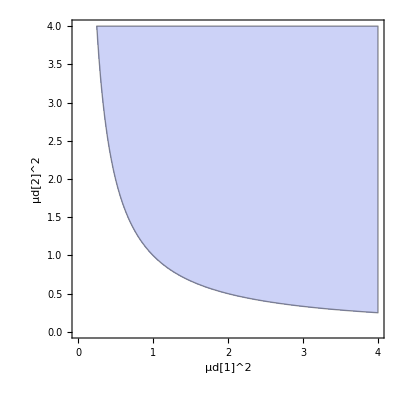

```mathematica
PR1["Another constraint comes from requiring the EWSB be preserved. ",
tmpv={{vd[1]},{vd[2]}}," and mass matrix: ",
(tmpμ={{μd[1]^2,μd[3]^2},{μd[3]^2,μd[2]^2}})//MatrixForms,check,Yield,
(tmp=xDot[Transpose[tmpv],tmpμ,tmpv])//MatrixForms,yield,
tmp=tmp/.xDot->Dot//Expand,NL,
"For stable V, Eigenvalues of mass matrix > 0 => Determinant > 0.",yield,
tmpβμ3=Det[tmpμ]>0
];
tmp=Eigenvalues[tmpμ]/.μd[3]->1//FullSimplify;
tmpc=Map[#>0&,tmp]/.{μd[3]->1,μd[1]^2->μ1,μd[2]^2->μ2};
tmpc=Apply[And,tmpc]
RegionPlot[tmpc,{μ1,0,4},{μ2,0,4},AxesLabel->{"μd[1]^2","μd[2]^2"}]
```

```mathematica
tmpc=tmpβμ1&&tmpβμ3/.{μd[3]->1,μd[1]^2->μ1,μd[2]^2->μ2}
RegionPlot[tmpc,{μ1,0,4},{μ2,0,4},AxesLabel->{"μd[1]^2","μd[2]^2"}]
```

1/(μ1+μ2)≤1/2&&-1+μ1 μ2>0

-Graphics-

{1/(μ1+μ2)==1/2,-1+μ1 μ2==0}

{2-μ1,1/μ1}

((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)==Cos[β] Sin[β]

((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)==Cos[β] Cos[β].Tan[β]

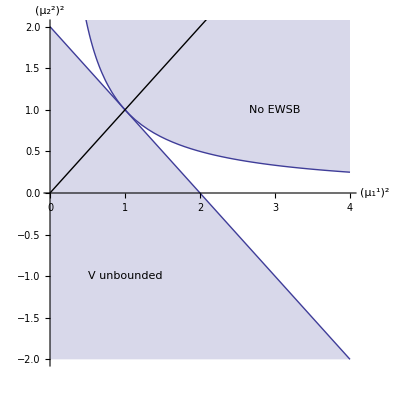

```mathematica
tmpc={tmpβμ1,tmpβμ3}/.{μd[3]->1,μd[1]^2->μ1,μd[2]^2->μ2,LessEqual->Equal,Greater->Equal}
tmp=Map[Solve[#/.Equal[a_,b_]->Equal[a-b,0],μ2][[1,1,2]]&,tmpc]
tmp1=tmpβμ//TrigExpand
tmp1/.Sin[β]->Cos[β].Tan[β]

Show[
{Plot[tmp[[1]],{μ1,0,4},Filling->Bottom],
Plot[tmp[[2]],{μ1,0,4},Filling->Top],
Graphics[{Line[{{0,0},{4,4}}],
Text["No EWSB",{3,1}],
Text["V unbounded",{1,-1}]
}]
},
AspectRatio->1,AxesLabel->{μd[1]^2,μd[2]^2}
]
```